```mathematica
Clear[σ,γ,v,G,L,V,fG,fL,fV,Vint]
G[x_,σ_]:=Exp[-x^2/(2 σ^2)]/(σ √(2π))
L[x_,γ_]:=γ/(π(x^2+γ^2))
V[x_,σ_,γ_]:=NIntegrate[G[y,σ]L[x-y,γ],{y,-∞,∞}]
fG[σ_]:=2σ √(2Log[2])
fL[γ_]:=2γ
fV[σ_,γ_]:=0.5346fL[γ]+√(0.2166 fL[γ]^2+fG[σ]^2)
Vint[σ_,γ_,v_]:=NIntegrate[V[x,σ,γ],{x,-v,v}]
```

NIntegrate::inumr: The integrand 0.0126987\ ⅇ^-0.125\ y^2/0.04  + (x - y)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 0.}}.

NIntegrate::inumr: The integrand 0.0126987\ ⅇ^-0.125\ y^2/0.04  + (-x - y)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

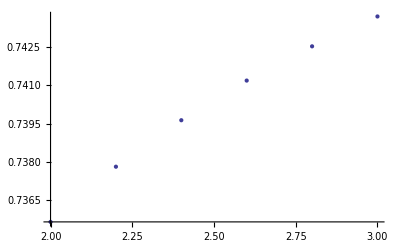

```mathematica
Clear[σ,γ,v]
γ=0.2;
(*Plot[V[x],{x,-1,1}]*)
(*NIntegrate[G[x],{x,-fG/2,fG/2}]*)
(*NIntegrate[L[x],{x,-fL/2,fL/2}]*)
data=Table[{σ,Vint[σ,γ,fV[σ,γ]/2]},{σ,2,3,0.2}];
ListPlot[data]
```